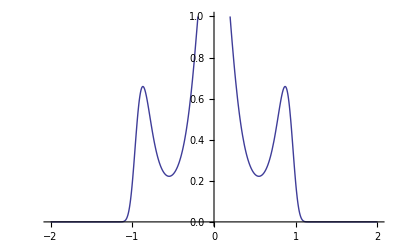

```mathematica
b=36.55 ;

d=-15.77 ;

f=0.5576 ;
g=-23.01 ;

F[x_]:=Exp[g x^6+b x^4+d x^2+f]
Plot[F[x],{x,-2,2},PlotRange->{{-2,2},{0,1}}]
```

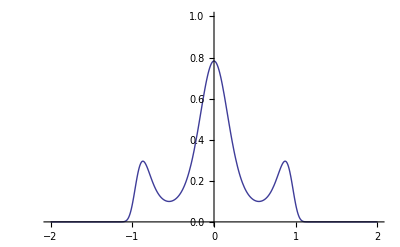

```mathematica
Plot[F[x],{x,-2,2},PlotRange->{{-2,2},{0,1}}]
```

```mathematica
NIntegrate[F[x],{x,-2,2}]
```

1.28127

```mathematica
fx=f;
fy=f/.{x->y}
Plot3D[fx fy,{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,1.2}}]
```

0.452451 ⅇ^(0.9576-2.189×10^-6 y-15.77 y^2+0.00002304 y^3+36.55 y^4-0.00002492 y^5-22.01 y^6)

-Graphics3D-

```mathematica
f
```

0.452451 ⅇ^(0.9576-2.189×10^-6 x-15.77 x^2+0.00002304 x^3+36.55 x^4-0.00002492 x^5-22.01 x^6)

```mathematica
NIntegrate[1 x^2 y^2 fx fy,{x,-2,2},{y,-2,2}]
```

0.100082

```mathematica
t=0.1;
j=-0.9;
F[x] F[y]/.{{x->t,y->j},{x->-t,y->j},{x->t,y->-j},{x->-t,y->-j}}
F[x] F[y]/.{{x->j,y->t},{x->-j,y->t},{x->j,y->-t},{x->-j,y->-t}}
```

{0.189203,0.189203,0.189203,0.189203}

{0.189203,0.189203,0.189203,0.189203}

```mathematica
G[x_,y_]:=F[Sqrt[x^2+y^2]]
```

```mathematica
t=0.1;
j=0.65;
G[x,y]/.{{x->t,y->j},{x->-t,y->j},{x->t,y->-j},{x->-t,y->-j}}
G[x,y]/.{{x->j,y->t},{x->-j,y->t},{x->j,y->-t},{x->-j,y->-t}}
```

{0.123718,0.123718,0.123718,0.123718}

{0.123718,0.123718,0.123718,0.123718}

```mathematica
Plot3D[G[x,y],{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,1.5}},Mesh->50]
```

```mathematica
NIntegrate[x^2 y^2 G[x,y],{x,-2,2},{y,-2,2}]
```

0.0576362

```mathematica
Gx[x_]:=(NIntegrate[G[x,y],{y,-2,2}])
Gy[y_]:=(NIntegrate[G[x,y],{x,-2,2}])
```

```mathematica
G[0.65,0.65]
Gx[0.65] Gy[0.65]
```

0.514517

0.218266

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.3320623332810648`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

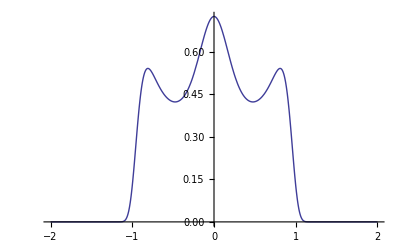

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.3320623332810648`}. NIntegrate obtained 0. and 0. for the integral and error estimates.

-Graphics-

```mathematica
Plot[Gx[x],{x,-2,2}]
Plot[Gy[y],{y,-2,2}]
```

```mathematica
G[1.5,1.5]
```

3.17593794878315×10^-581

```mathematica
G[x_,y_]:=1/1.4737549100730927 F[Sqrt[x^2+y^2]]
NIntegrate[ x^2y^2 G[x,y],{x,-2,2},{y,-2,2}]
Plot3D[G[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Mesh->50]
```

0.0442756

-Graphics3D-

```mathematica
Plot3D[1/17.330975561218562 Exp[-0.5(1x^4-2x^2+1y^4-2y^2)],{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,0.17}},Mesh->50]
Plot3D[1/4.1630488344513665 Exp[-0.5(x^4-2x^2)]1/4.1630488344513665Exp[-0.5(y^4-2y^2)],{x,-2,2},{y,-2,2},PlotRange->{{-2,2},{-2,2},{0,0.17}},Mesh->50]
```

-Graphics3D-

-Graphics3D-

```mathematica
NIntegrate[Exp[-0.5(x^4-2x^2+y^4-2y^2)],{x,-2,2},{y,-2,2}]
```

17.331

```mathematica
4.1630488344513665 4.1630488344513665
```

17.331

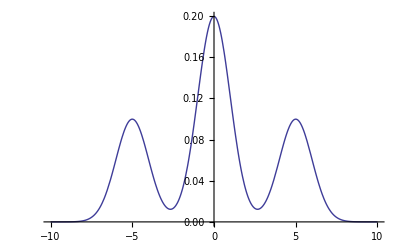

-Graphics3D-

```mathematica
NN[x_,m_]:=1/Sqrt[2 Pi] Exp[-0.5(x-m)^2];
P1[x_]:=0.5 NN[x,0]+0.25 NN[x,5]+0.25 NN[x,-5]
Plot[P1[x],{x,-10,10}]
Plot3D[P1[x]P1[y],{x,-10,10},{y,-10,10}]
```

```mathematica
t=0.1;
j=0.65;
G[x,y]/.{{x->t,y->j},{x->-t,y->j},{x->t,y->-j},{x->-t,y->-j}}
G[x,y]/.{{x->j,y->t},{x->-j,y->t},{x->j,y->-t},{x->-j,y->-t}}
```

```mathematica
NIntegrate[P1[x],{x,-10,10}]
```

1.

```mathematica
t=0.1;
j=0.65;
P1[x]P1[y]/.{{x->t,y->j},{x->-t,y->j},{x->t,y->-j},{x->-t,y->-j}}
P1[x]P1[y]/.{{x->j,y->t},{x->-j,y->t},{x->j,y->-t},{x->-j,y->-t}}
```

{0.0320529,0.0320529,0.0320529,0.0320529}

{0.0320529,0.0320529,0.0320529,0.0320529}